# Full Cell: The Big One!

## Parameters

This list has all of the parameters listed in the paper. Initial conditions were calculated externally and put directly into the NDSolve’s.

```mathematica
parameters={(*delayed rectifier*)gd->(*.35*).35,ek->-80,cn->180,vn->-25,vkn->10,sn->-17,skn->-22,(*transient A-like*)ga->2.2,ek->-80,ka->140,ka1->50,ca2->3.6,va->-12,vb->-62,va2->-40,vx->7,sa->-26,sb->6,sa2->-12,sx->-15,
(*ih*)gh->0.037,eh->-10,cr->0.33,vr->-70,vkr->-110,sr->7,skr->-13,(*sodium*)gna->2300,ena->50,km->10000,kh->500,vam->-6,vbm->-34,vah->-39,vbh->-40,sam->-20,sbm->-13,sah->-8,sbh->-5,cam->0.11,cbm->15,cah->0.08,(*inward calcium/buffer*)gca1->0.21,gca2->0.047,kaca1->50,kbca1->16,kaca2->10,vaca1->-11,vbca1->-50,vaca2->22,saca1->-7,sbca1->8,saca2->-7,
(*outward ca*)g0ca->3.2,ek->-80,koa->600,kob->35,kca->360,vao1->0,vao2->-16,sao1->-23,sao2->-5,f->0.6,c1->2.5,c2->0.7,c3->0.6,ca0->0.05,cica->300,(*leak, including cm*)gl->0.1,el->-50,cm->1700(*this value is converted from nF to micro Farads*)};
```

## Steady State Equations

This will go current-by-current, with all the steady states they define.

#### Delayed Rectifier

```mathematica
(*voltage dependence*)ninfinite[V_]:=1/(1+Exp[(V-vn)/sn])/.parameters;(*relaxation*)ka[V_]:=cn/(1+Exp[(V-vkn)/skn])/.parameters;
```

#### Ca2+ Outward

```mathematica
a0infinity[V_,Ca_]:=1/(1+Exp[(V-vao1+f*Ca)/sao1])*1/(1+Exp[(V-vao2+f*Ca)/sao2])*(Ca/(c1+Ca))/.parameters;
b0infinity[Ca_]:=c2/(c3+Ca)/.parameters;
```

#### Transient A-Like

```mathematica
aainfinite[V_]:=1/(1+Exp[(V-va)/sa])/.parameters;
(*inactivation 1*)
kbinfinite[V_]:=1/(1+Exp[(V-vb)/sb])/.parameters;
(*steady states: inactivation 2*)
ka2infinite[V_]:=1/(1+Exp[(V-va2)/sa2])/.parameters;
ka2relaxation[V_]:=ca2/(1+Exp[(V-va2)/sa2])/.parameters;
(*weighting factor*)
x[V_]:=1/(1+Exp[(V-vx)/sx])/.parameters;
```

#### Ca2+ (Inward)

```mathematica
(*nernst potential*)eCa[Ca_]:=((8.314*283)/(2*96485.3329))*Log[(13000/Ca)]*1000;
aca1VoltDep[V_]:=1/(1+Exp[(V-vaca1)/saca1])/.parameters;baca1VoltDep[V_]:=1/(1+Exp[(V-vbca1)/sbca1])/.parameters;aca2VoltDep[V_]:=1/(1+Exp[(V-vaca2)/saca2])/.parameters;
```

#### Inwardly Rectifying/Hyperpolarization Activated

```mathematica
(*Voltage Dependence*)
rinfinite[V_]:=1/(1+Exp[(V-vr)/sr])/.parameters;
(*relaxation*)
kr[V_]:=cr*(1+Exp[(V-vkr)/skr])/.parameters;
```

#### Fast Na+

```mathematica
(*steady states: activation*)
minfinite[V_]:=am[V]/(am[V]+bm[V])/.parameters;
am[V_]:=cam(V-vam)/(1-Exp[(V-vam)/sam])/.parameters;
bm[V_]:=cbm Exp[(V-vbm)/sbm]/.parameters;

(*steady states: inactivation*)
hinfinite[V_]:=ah[V]/(ah[V]+bh[V])/.parameters;
ah[V_]:=cah*Exp[(V-vah)/sah]/.parameters;
bh[V_]:=1/(1+Exp[(V-vbh)/sbh])/.parameters;
```

### Pulse Eq

Some explanation: no pulse equation is mentioned in the paper, but Dr. Chiel suggested it as a first step to become comfortable with the model. Here’s how it is defined in chapter 7 of the textbook. 
Hillel (2019). 7. Modeling Excitability: Rhythmic Behavior and Bistability. Dynamics of Biological Systems: A Quantitative Introduction to Biology.

```mathematica
pulse[t_,A_,ton_,toff_]:= A(UnitStep[t-ton]-UnitStep[t-toff]);
```

## The Cell

The cell is built up in steps, adding specific currents to get specific behaviors.

### Leak and Pulse

We can get spiking behavior from the leak and the pulse! Admittedly, the spiking is simply the pulse.

```mathematica
leakPulseEq=NDSolve[{1.7(*original value*)*V'[t]==pulse[t,10,.1,.2]-gl*(V[t]-el),V[0]==-45}/.parameters,V[t],{t,0,0.4}];
```

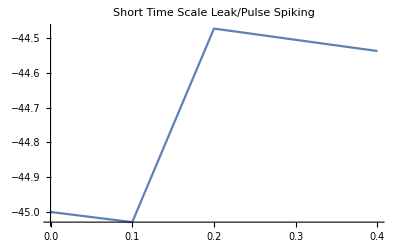

```mathematica
leakPulsePlot=Plot[Evaluate[V[t]/.leakPulseEq/.parameters],{t,0,0.4(*the paper's time scale*)},PlotRange->All,PlotLabel->"Short Time Scale Leak/Pulse Spiking"]
```

Let’s try this with the other pulse definition. This one includes more parameters and allows for multiple pulses to be generated:

```mathematica
pulseFullParam[t_,t0_,w_,p_,D_,A_]:= A(Sum[UnitStep[t-i] - UnitStep[t-(i+w)],{i,t0,t0+D,p}])
```

```mathematica
leakMultiplePulse=NDSolve[{1.7*V'[t]==pulseFullParam[t,25,5,25,100,10]-gl*(V[t]-el),V[0]==-45}/.parameters,V[t],{t,0,200(*longer time scale makes it easier to see this*)}];
```

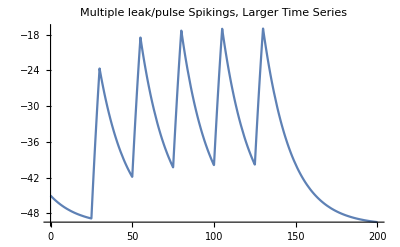

```mathematica
leakMultiplePulsePlot=Plot[Evaluate[V[t]/.leakMultiplePulse[[1,All]]],{t,0,200},PlotRange->All,PlotLabel->"Multiple leak/pulse Spikings, Larger Time Series"]
```

### Add Idr and Ina

let’s add the delayed rectifier and sodium currents.

set up manipulate to change relative sizes of pot. and sodium to get repetitive firing. (gd and gna)

we should be able to obtain repetitive firing on this graph after a single pulse. Set drCond->3.5, and naCond->4600 to see this behavior.

```mathematica
leakPulseDrNa=Manipulate[Plot[Evaluate[V[t]/.NDSolve[{1.7(*capacitance given in paper*)*V'[t]==pulse[t,10,10,pulseEnd]
-(*leak*)(gl*(V[t]+50)
+(*sodium*)(naCond*m[t]^3*h[t]*(V[t]-50))
+(*delayed rectifier*)(drCond*(n[t])^4*(V[t]+80))),
n'[t]==(ninfinite[V[t]]-n[t])*ka[V[t]],n[0]==0.29269,m'[t]==(minfinite[V[t]]-m[t])*(am[V[t]]+bm[V[t]]),
m[0]==0.03393532895134747,
h'[t]==(hinfinite[V[t]]-h[t])*(ah[V[t]]+bh[V[t]]),
h[0]==0.15347767422936445,V[0]==-45}/.parameters,{V[t],n[t],m[t],h[t]},{t,0,400(*note that the paper's time series offers no noticeable behavior*)}]],{t,0,400},PlotRange->{{0,200},{-50,50}},AxesOrigin->{0,0}],{{drCond,0.35},0.0035,350},{{naCond,2300},575,4600},{{pulseEnd,20},10,200}]
```

### Add Ih

```mathematica
leakPulseDrNaH=NDSolve[{1.7*V'[t]==pulse[t,10,10,20]
-(*leak*)(gl*(V[t]+50)
+(*sodium*)(2*gna*m[t]^3*h[t]*(V[t]-50))
+(*delayed rectifier*)(10*gd*(n[t])^4*(V[t]+80))
+(*hyperpolarized-activated*)(gh*(r[t])*(V[t]-eh))),
n'[t]==(ninfinite[V[t]]-n[t])*ka[V[t]],n[0]==0.29269,m'[t]==(minfinite[V[t]]-m[t])*(am[V[t]]+bm[V[t]]),
m[0]==0.03393532895134747,
h'[t]==(hinfinite[V[t]]-h[t])*(ah[V[t]]+bh[V[t]]),
h[0]==0.15347767422936445,
r'[t]==(rinfinite[V[t]]-r[t])*kr[V[t]],
r[0]==0.013576916943744367,
V[0]==-45}/.parameters,{V[t],n[t],m[t],h[t],r[t]},{t,0,400}];
```

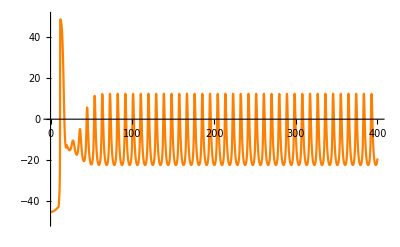

```mathematica
leakPulseDrNaHPlot=Plot[Evaluate[V[t]/.leakPulseDrNaH[[1,All]]],{t,0,400},PlotRange->{{0,400},{-50,50}},PlotStyle->Orange]
```

### Add Ica (inward)

```mathematica
leakPulseDrNaHCa=NDSolve[{1.7*V'[t]==pulse[t,10,25,50]
-(*leak*)(gl*(V[t]+50)
+(*sodium*)(2*gna*m[t]^3*h[t]*(V[t]-50))
+(*delayed rectifier*)(10*gd*(n[t])^4*(V[t]+80))
+(*hyperpolarized-activated*)(gh*(r[t])*(V[t]-eh))
+(*inward calcium*)(((gca1*aca1[t]*baca1[t])+(gca2*aca2[t]))*(V[t]-eCa[Ca[t]]))),
n'[t]==(ninfinite[V[t]]-n[t])*ka[V[t]],n[0]==0.29269,m'[t]==(minfinite[V[t]]-m[t])*(am[V[t]]+bm[V[t]]),
m[0]==0.03393532895134747,
h'[t]==(hinfinite[V[t]]-h[t])*(ah[V[t]]+bh[V[t]]),
h[0]==0.15347767422936445,
r'[t]==(rinfinite[V[t]]-r[t])*kr[V[t]],
r[0]==0.013576916943744367,
aca1'[t]==(aca1VoltDep[V[t]]-aca1[t])*kaca1,
aca1[0]==0.015629270047407037,
baca1'[t]==(baca1VoltDep[V[t]]-baca1[t])*kbca1,
baca1[0]==0.22270013882530884,
aca2'[t]==(aca2VoltDep[V[t]]-aca2[t])*kaca2,
aca2[0]==0.000142340966186228,
(*calcium buffer*)Ca'[t]==-cica*(((gca1*aca1[t]*baca1[t])+(gca2*aca2[t]))*(V[t]-eCa[Ca[t]]))-kca*Ca[t]+kca*ca0,Ca[0]==0.15934876118185337+ca0,
V[0]==-45}/.parameters,{V[t],n[t],m[t],h[t],r[t]},{t,0,400}];
```

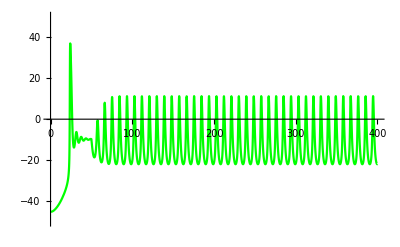

```mathematica
leakPulseDrNaHCaPlot=Plot[Evaluate[V[t]/.leakPulseDrNaHCa[[1,All]]],{t,0,400},PlotRange->{{0,400},{-50,50}},PlotStyle->Green]
```

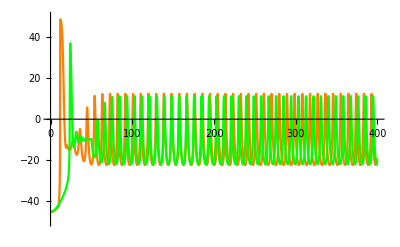

```mathematica
(*let's see these plots on top of each other*)
Show[leakPulseDrNaHPlot,leakPulseDrNaHCaPlot]
```

### The Full Cell (not working with IA)

By commenting out IA, I am able to obtain proper behavior. Look below at figure 4A to see the graph of IA. It isn’t quite right, either.

```mathematica
LP=NDSolve[{1.7*V'[t]==(*calcium currents*)-((g0ca*a0[t]*b0[t]*(V[t]-ek))+
(((gca1*aca1[t]*baca1[t])+(gca2*aca2[t]))*(V[t]-eCa[Ca[t]]))
+(*dr*)(10*gd*(n[t])^4*(V[t]-ek))+
(*na*)(2*gna*m[t]^3*h[t]*(V[t]-ena))+
(*ih*)(gh*(r[t])*(V[t]-eh))+
(*(*iA*)(ga*(aa[t])^3*(x[V[t]]*ba1[t]+(1-x[V[t]])*ba2[t])*(V[t]-ek))+*)
(*leak*)gl*(V[t]-el)),
(*iA act/inact*)aa'[t]==(aainfinite[V[t]]-aa[t])*ka,ba1'[t]==(kbinfinite[V[t]]-ba1[t])*ka1,ba2'[t]==(ka2infinite[V[t]]-ba2[t])*(ka2relaxation[V[t]]),aa[0]==0.25408873728969605,ba1[0]==0.02492442664711404,ba2[0]==0.5,
(*ih act/inact*)r'[t]==(rinfinite[V[t]]-r[t])*kr[V[t]],r[0]==0.013576916943744367,(*id act/inact*)n'[t]==(ninfinite[V[t]]-n[t])*ka[V[t]],n[0]==0.29269,
(*calcium currents*)a0'[t]==(a0infinity[V[t],Ca[t]]-a0[t])*koa,a0[0]==0.00007448265106619814,b0'[t]==(b0infinity[Ca[t]]-b0[t])*kob,b0[0]==0.9218425521765746,aca1'[t]==(aca1VoltDep[V[t]]-aca1[t])*kaca1,baca1'[t]==(baca1VoltDep[V[t]]-baca1[t])*kbca1,
aca2'[t]==(aca2VoltDep[V[t]]-aca2[t])*kaca2,
aca2[0]==0.000142340966186228,aca1[0]==0.015629270047407037,baca1[0]==0.22270013882530884,(*calcium buffer*)Ca'[t]==-cica*(((gca1*aca1[t]*baca1[t])+(gca2*aca2[t]))*(V[t]-eCa[Ca[t]]))-kca*Ca[t]+kca*ca0,Ca[0]==0.15934876118185337+ca0,
(*ina act/inact*)m'[t]==(minfinite[V[t]]-m[t])*(am[V[t]]+bm[V[t]]),m[0]==0.03393532895134747,h'[t]==(hinfinite[V[t]]-h[t])*(ah[V[t]]+bh[V[t]]),h[0]==0.15347767422936445,V[0]==-45(*not sure if this is right*)}/.parameters,{V[t],aa[t],ba1[t],ba2[t],r[t],n[t],a0[t],b0[t],aca1[t],baca1[t],aca2[t],Ca[t],m[t],h[t]},{t,0,400}];
```

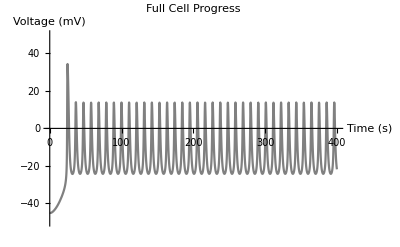

```mathematica
lpPlot=Plot[V[t]/.LP[[1,All]]/.parameters,{t,0,400},PlotRange->{{0,400},{-50,50}},PlotStyle->Gray,AxesLabel->{"Time (s)","Voltage (mV)"},PlotLabel->"Full Cell Progress"]
```

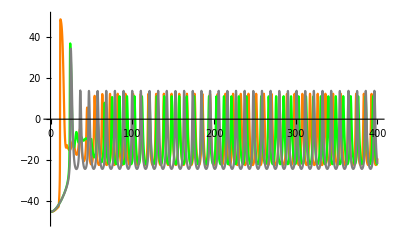

```mathematica
Show[leakPulseDrNaHPlot,leakPulseDrNaHCaPlot,lpPlot]
```

### Attempt at Fig 6

I’m going to try just plotting the conductance equation over V from -150 to 100, putting in the steady state equations for acts/inacts.

```mathematica
fig6Id=Plot[id[V]=(gd*(ninfinite[V])^4*(V-ek))/.parameters,{V,-150,100},PlotRange->{{-150,100},{-30,75}},AxesOrigin->{-150,-30}];
```

```mathematica
fig6Ina=Plot[ina[V]=(gna*(minfinite[V])^3*hinfinite[V]*(V-ena))/.parameters,{V,-150,100},PlotRange->{{-150,100},{-30,75}},AxesOrigin->{-150,-30},PlotStyle->Orange];
```

```mathematica
fig6Ih=Plot[ih[V]=(gh*rinfinite[V]*(V-eh))/.parameters,{V,-150,100},PlotRange->{{-150,100},{-30,75}},AxesOrigin->{-150,-30},PlotStyle->Green];
```

```mathematica
fig6IA=Plot[iA[V]=(ga*aainfinite[V]^3*(x[V]*kbinfinite[V]+(1-x[V])*ka2infinite[V])*(V-ek))/.parameters,{V,-150,100},PlotRange->{{-150,100},{-30,75}},AxesOrigin->{-150,-30},PlotStyle->{Black,Dashed}];
```

```mathematica
fig6Il=Plot[il[V]=(gl*(V-el))/.parameters,{V,-150,100},PlotRange->{{-150,100},{-30,75}},AxesOrigin->{-150,-30},PlotStyle->Black];
```

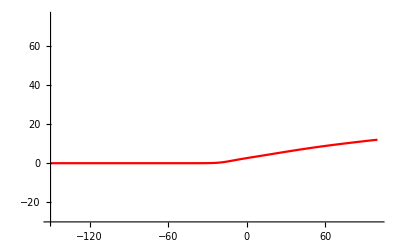

```mathematica
fig6I0Ca=Plot[i0Ca[V]=(g0ca*a0infinity[V,ca0]*b0infinity[ca0]*(V-ek))/.parameters,{V,-150,100},PlotRange->{{-150,100},{-30,75}},AxesOrigin->{-150,-30},PlotStyle->Red](*this one is a bit of a problem area*)
```

```mathematica
fig6Ica=
Plot[iCa[V]=(((gca1*aca1VoltDep[V]*baca1VoltDep[V])+(gca2*aca2VoltDep[V]))*(V-eCa[ca0]))/.parameters,{V,-150,100},PlotRange->{{-150,100},{-30,75}},PlotStyle->Purple];
```

## Figure 1

### A

```mathematica
{dr40,dr30,dr20,dr10,dr0,drneg10,drneg20,drneg30,drneg40,drneg50}=Table[NDSolve[{cm*V'[t]==(-(gd*(n[t])^4*(V[t]-ek))),n'[t]==(ninfinite[V[t]]-n[t])*ka[V[t]],V[0]==initV,n[0]==0.29269}/.parameters,{V[t],n[t]},{t,0,.3}],{initV,{40,30,20,10,0,-10,-20,-30,-40,-50}}];
```

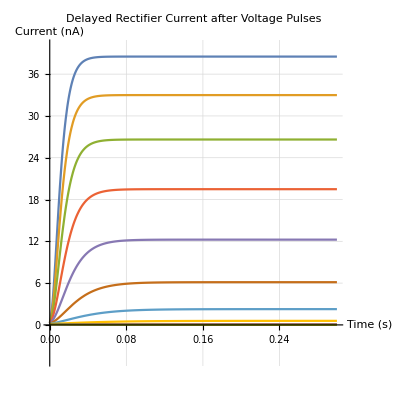

```mathematica
Plot[{Evaluate[.35*n[t]^4*(V[t]+80)/.dr40[[1,All]]/.parameters],Evaluate[.35*n[t]^4*(V[t]+80)/.dr30[[1,All]]/.parameters],Evaluate[0.35*n[t]^4*(V[t]+80)/.dr20[[1,All]]/.parameters],Evaluate[0.35*n[t]^4*(V[t]+80)/.dr10[[1,All]]/.parameters],Evaluate[0.35*n[t]^4*(V[t]+80)/.dr0[[1,All]]/.parameters],Evaluate[0.35*n[t]^4*(V[t]+80)/.drneg10[[1,All]]/.parameters],Evaluate[0.35*n[t]^4*(V[t]+80)/.drneg20[[1,All]]/.parameters],Evaluate[0.35*n[t]^4*(V[t]+80)/.drneg30[[1,All]]/.parameters],Evaluate[0.35*n[t]^4*(V[t]+80)/.drneg40[[1,All]]/.parameters],Evaluate[0.35*n[t]^4*(V[t]+80)/.drneg50[[1,All]]/.parameters]},{t,0,.3},PlotRange->{{0,.3},{-5,40}},GridLines->Automatic,AxesLabel->{"Time (s)","Current (nA)"},PlotLabel->"Delayed Rectifier Current after Voltage Pulses",AspectRatio->1]
```

### B

```mathematica
drActVoltDep=Plot[1/(1+Exp[(V+25)/(-17)]),{V,-80,80},AxesLabel->{"Voltage","Normalized Values"},GridLines->Automatic];drNormRelax=Plot[cn/(1+Exp[(V-vkn)/skn])/ka[80]/.parameters,{V,-80,80},AxesLabel->{"Voltage","Relaxation"},PlotStyle->Orange];
```

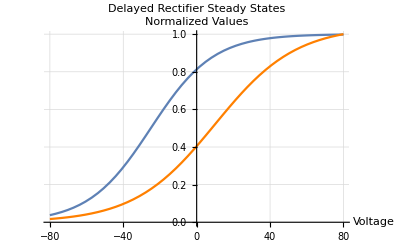

```mathematica
Show[drActVoltDep,drNormRelax,PlotLabel->"Delayed Rectifier Steady States"]
```

## Figure 2

### A

```mathematica
{caOutNeg30,caOutNeg20,caOutNeg10,caOut0,caOut10,caOut20}=Table[NDSolve[{Ca'[t]==-cica*(((gca1*aca1[t]*baca1[t])+(gca2*aca2[t]))*(V[t]-eCa[Ca[t]]))-kca*Ca[t]+kca*ca0,aca1'[t]==(aca1VoltDep[V[t]]-aca1[t])*kaca1,baca1'[t]==(baca1VoltDep[V[t]]-baca1[t])*kbca1,
aca2'[t]==(aca2VoltDep[V[t]]-aca2[t])*kaca2,Ca[0]==0.15934876118185337+ca0,
aca2[0]==0.000142340966186228,aca1[0]==0.015629270047407037,baca1[0]==0.22270013882530884,1700*V'[t]==-((g0ca*a0[t]*b0[t]*(V[t]-ek))+(((gca1*aca1[t]*baca1[t])+(gca2*aca2[t]))*(V[t]-eCa[Ca[t]]))),a0'[t]==(a0infinity[V[t],Ca[t]]-a0[t])*koa,a0[0]==0.00007448265106619814,b0'[t]==(b0infinity[Ca[t]]-b0[t])*kob,b0[0]==0.9218425521765746,V[0]==initV}/.parameters,{Ca[t],aca1[t],aca2[t],baca1[t],V[t],a0[t],b0[t]},{t,0,100000}],{initV,{-30,-20,-10,0,10,20}}];
```

```mathematica
(*side note: the Calcium concentration plot*)Plot[{Ca[t]/.caOutNeg30[[1,All]],Ca[t]/.caOutNeg20[[1,All]],Ca[t]/.caOutNeg10[[1,All]],Ca[t]/.caOut0[[1,All]],Ca[t]/.caOut10[[1,All]],Ca[t]/.caOut20[[1,All]]},{t,0,0.175},PlotRange->{{0,.175},{0,3}},GridLines->Automatic];
```

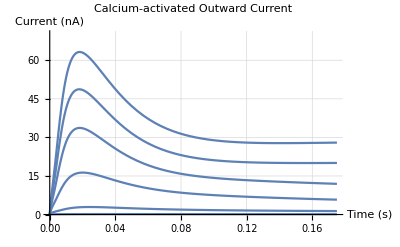

```mathematica
Plot[{g0ca*a0[t]*b0[t]*(V[t]-ek)/.caOutNeg30[[1,All]],g0ca*a0[t]*b0[t]*(V[t]-ek)/.caOutNeg20[[1,All]],g0ca*a0[t]*b0[t]*(V[t]-ek)/.caOutNeg10[[1,All]],g0ca*a0[t]*b0[t]*(V[t]-ek)/.caOut0[[1,All]],g0ca*a0[t]*b0[t]*(V[t]-ek)/.caOut10[[1,All]],g0ca*a0[t]*b0[t]*(V[t]-ek)/.caOut20[[1,All]]}/.parameters,{t,0,.175},PlotRange->{{0,.175},{-3,70}},GridLines->Automatic,AxesLabel->{"Time (s)","Current (nA)"},PlotLabel->"Calcium-activated Outward Current"]
```

### B

```mathematica
{a0Plot100,a0Plot50,a0Plot5,a0PlotHalf,a0PlotTwentieth} =Table[Plot[a0infinity[V,CaVal]/.parameters,{V,-100,100},PlotRange->{{-100,100},{0,1}},GridLines->Automatic,AxesLabel->{"Voltage (mV)","a0infinity (no units"}],{CaVal,{100,50,5,0.5,0.05}}];
```

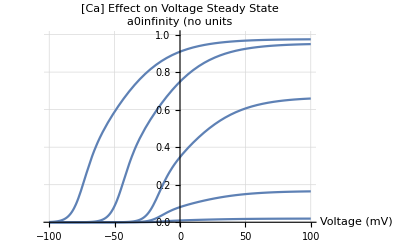

```mathematica
Show[a0Plot100,a0Plot50,a0Plot5,a0PlotHalf,a0PlotTwentieth,PlotLabel->"[Ca] Effect on Voltage Steady State"]
```

### C

```mathematica
{normCond30,normCond20,normCond10,normCond0,normCondNeg10}=Table[Plot[a0infinity[V,Ca]*b0infinity[Ca]/.parameters,{Ca,0,20},PlotRange->{{0,20},{0,0.12}},AxesLabel->{"[Ca] (uM)","normalized g0(Ca)"}],{V,{30,20,10,0,-10}}];
```

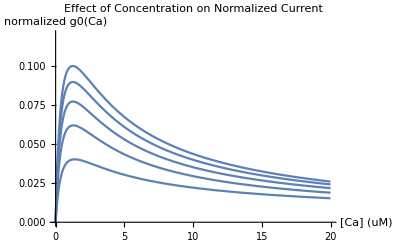

```mathematica
Show[normCond30,normCond20,normCond10,normCond0,normCondNeg10,PlotLabel->"Effect of Concentration on Normalized Current"]
```

## Figure 3

### A

```mathematica
{aneg40,aneg30,aneg20,aneg10,a00,a10}=Table[NDSolve[{1.7(*original value*)*V'[t]==(-(ga*(aa[t]^3)*(x[V[t]]*ba1[t]+(1-x[V[t]])*ba2[t])*(V[t]-ek))),aa'[t]==(aainfinite[V[t]]-aa[t])*ka,ba1'[t]==(kbinfinite[V[t]]-ba1[t])*ka1,ba2'[t]==(ka2infinite[V[t]]-ba2[t])*(ka2relaxation[V[t]]),V[0]==initV,aa[0]==0.25408873728969605,ba1[0]==0.02492442664711404,ba2[0]==0.5}/.parameters,{V[t],aa[t],ba1[t],ba2[t]},{t,0,0.3}],{initV,{-40,-30,-20,-10,0,10}}];
```

### B

ReplaceAll::reps: {a0⟦1,All⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

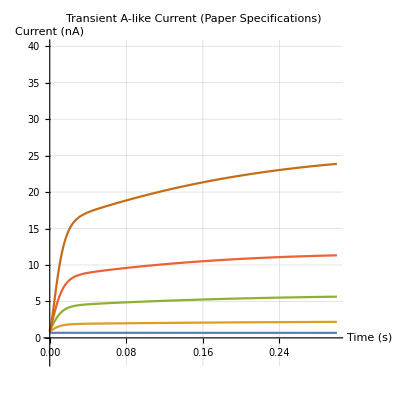

```mathematica
Plot[{Evaluate[2.2*aa[t]^3*(x[V[t]]*ba1[t]+(1-x[V[t]])*ba2[t])*(V[t]-ek)/.aneg40[[1,All]]/.parameters],Evaluate[2.2*aa[t]^3*(x[V[t]]*ba1[t]+(1-x[V[t]])*ba2[t])*(V[t]-ek)/.aneg30[[1,All]]/.parameters],Evaluate[2.2*aa[t]^3*(x[V[t]]*ba1[t]+(1-x[V[t]])*ba2[t])*(V[t]-ek)/.aneg20[[1,All]]/.parameters],Evaluate[2.2*aa[t]^3*(x[V[t]]*ba1[t]+(1-x[V[t]])*ba2[t])*(V[t]-ek)/.aneg10[[1,All]]/.parameters],Evaluate[2.2*aa[t]^3*(x[V[t]]*ba1[t]+(1-x[V[t]])*ba2[t])*(V[t]-ek)/.a0[[1,All]]/.parameters],Evaluate[2.2*aa[t]^3*(x[V[t]]*ba1[t]+(1-x[V[t]])*ba2[t])*(V[t]-ek)/.a10[[1,All]]/.parameters]},{t,0,0.3},PlotRange->{{0,0.3},{-3,40}},GridLines->Automatic,AxesLabel->{"Time (s)","Current (nA)"},PlotLabel->"Transient A-like Current (Paper Specifications)",AspectRatio->1]
```

## Figure 4

### A

```mathematica
{hneg120,hneg110,hneg100,hneg90,hneg80,hneg70}=Table[NDSolve[{cm*V'[t]==(-(gh*(r[t])*(V[t]-eh))),r'[t]==(rinfinite[V[t]]-r[t])*kr[V[t]],r[0]==0.013576916943744367,V[0]==initV}/.parameters,{V[t],r[t]},{t,0,20}],{initV,{-120,-110,-100,-90,-80,-70}}];
```

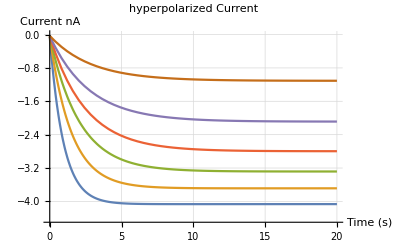

```mathematica
Plot[{Evaluate[.037*r[t]*(V[t]+10)/.hneg120[[1,All]]/.parameters],Evaluate[.037*r[t]*(V[t]+10)/.hneg110[[1,All]]/.parameters],Evaluate[.037*r[t]*(V[t]+10)/.hneg100[[1,All]]/.parameters],Evaluate[.037*r[t]*(V[t]+10)/.hneg90[[1,All]]/.parameters],Evaluate[.037*r[t]*(V[t]+10)/.hneg80[[1,All]]/.parameters],Evaluate[.037*r[t]*(V[t]+10)/.hneg70[[1,All]]/.parameters]},{t,0,20},PlotRange->{{0,20},{-4.5,0}},GridLines->Automatic,AxesLabel->{"Time (s)","Current nA"},PlotLabel->"hyperpolarized Current",AxesOrigin->{0,-4.5}]
```

### B

```mathematica
hVoltDep=Plot[1/(1+Exp[(V+70)/7]),{V,-150,-25},AxesLabel->{"Voltage (mV)","Conductance"},PlotRange->{{-150,-25},{0,1}},GridLines->Automatic];
hNormRelax=Plot[Evaluate[kr[V]]/kr[-150]/.parameters,{V,-150,-25},PlotRange->{{-150,-25},{0,1}},PlotStyle->Orange];
```

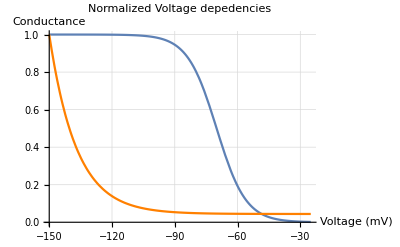

```mathematica
Show[hVoltDep,hNormRelax,PlotLabel->"Normalized Voltage depedencies"]
```

## Figure 5

### B

## Figure 6

### A

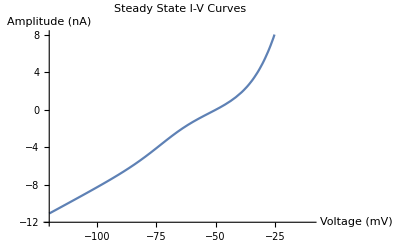

```mathematica
(*na is removed*)fig6A=Plot[lpFull[V]=(gd*(ninfinite[V])^4*(V-ek)
+gh*rinfinite[V]*(V-eh)
+ga*aainfinite[V]^3*(x[V]*kbinfinite[V]+(1-x[V])*ka2infinite[V])*(V-ek)
+gl*(V-el)
+3.2*a0infinity[V,ca0]*b0infinity[ca0]*(V+80)
+((gca1*aca1VoltDep[V]*baca1VoltDep[V])+(gca2*aca2VoltDep[V]))*(V-eCa[ca0]))/.parameters,{V,-120,-10},PlotRange->{{-120,-10},{-12,8}},AxesOrigin->{-120,-12},AxesLabel->{"Voltage (mV)","Amplitude (nA)"},PlotLabel->"Steady State I-V Curves"]
```

### B

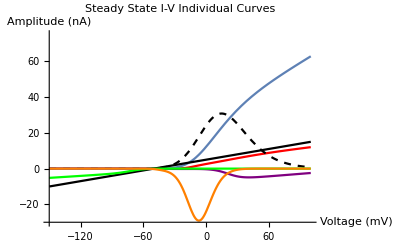

```mathematica
Show[fig6I0Ca,fig6IA,fig6Ica,fig6Id,fig6Il,fig6Ih,fig6Ina,PlotLabel->"Steady State I-V Individual Curves",AxesLabel->{"Voltage (mV)","Amplitude (nA)"}]
```

## Figure 7

## Extension Work

```mathematica
LPManipulate=Manipulate[Plot[Evaluate[V[t]/.NDSolve[{cmVal*V'[t]==(*calcium currents*)-((g0caVal*a0[t]*b0[t]*(V[t]-ek))+
(((gca1*aca1[t]*baca1[t])+(gca2*aca2[t]))*(V[t]-eCa[Ca[t]]))
+(*dr*)(gdVal*(n[t])^4*(V[t]-ek))+
(*na*)(gnaVal*m[t]^3*h[t]*(V[t]-ena))+
(*ih*)(ghVal*(r[t])*(V[t]-eh))+
(*iA*)(gaVal*(aa[t])^3*(x[V[t]]*ba1[t]+(1-x[V[t]])*ba2[t])*(V[t]-ek))+
(*leak*)(glVal*(V[t]-el))),
(*iA act/inact*)aa'[t]==(aainfinite[V[t]]-aa[t])*ka,ba1'[t]==(kbinfinite[V[t]]-ba1[t])*ka1,ba2'[t]==(ka2infinite[V[t]]-ba2[t])*(ka2relaxation[V[t]]),aa[0]==0.25408873728969605,ba1[0]==0.02492442664711404,ba2[0]==0.5,
(*ih act/inact*)r'[t]==(rinfinite[V[t]]-r[t])*kr[V[t]],r[0]==0.013576916943744367,(*id act/inact*)n'[t]==(ninfinite[V[t]]-n[t])*ka[V[t]],n[0]==0.29269,
(*calcium currents*)a0'[t]==(a0infinity[V[t],Ca[t]]-a0[t])*koa,a0[0]==0.00007448265106619814,b0'[t]==(b0infinity[Ca[t]]-b0[t])*kob,b0[0]==0.9218425521765746,aca1'[t]==(aca1VoltDep[V[t]]-aca1[t])*kaca1,baca1'[t]==(baca1VoltDep[V[t]]-baca1[t])*kbca1,
aca2'[t]==(aca2VoltDep[V[t]]-aca2[t])*kaca2,
aca2[0]==0.000142340966186228,aca1[0]==0.015629270047407037,baca1[0]==0.22270013882530884,(*calcium buffer*)Ca'[t]==-cica*(((gca1*aca1[t]*baca1[t])+(gca2*aca2[t]))*(V[t]-eCa[Ca[t]]))-kca*Ca[t]+kca*ca0,Ca[0]==0.15934876118185337+ca0,
(*ina act/inact*)m'[t]==(minfinite[V[t]]-m[t])*(am[V[t]]+bm[V[t]]),m[0]==0.03393532895134747,h'[t]==(hinfinite[V[t]]-h[t])*(ah[V[t]]+bh[V[t]]),h[0]==0.15347767422936445,V[0]==initV}/.parameters,{V[t],aa[t],ba1[t],ba2[t],r[t],n[t],a0[t],b0[t],aca1[t],baca1[t],aca2[t],Ca[t],m[t],h[t]},{t,0,400}]],{t,0,400},PlotRange->{{0,400},{-50,50}},AxesLabel->{"Time (s)","Voltage (mV)"},AxesOrigin->{0,-50}],{{gdVal,0.35},0,35},{{gnaVal,2300},0,4600},{{ghVal,0.037},0,37},{{g0caVal,3.2},0,320},{{gaVal,2.2},0,220},{{glVal,0.1},0,10},{{cmVal,1.7},0.17,1700},{{initV,-45},-40,-50}]
```

Observations

2.2 seems too high for the transient A-like - that value causes it to dominate the model cell. Setting it to 0.22 allows it to have impact without dominating.

The ratio between the delayed rectifier and sodium currents initially looks completely out of whack. We definitely need to increase the influence of the delayed rectifer, but we actually need to increase the sodium as well. It may be possible that the sodium equations are incorrect in some way and thus giving values that need to be overcorrected. This is the one current in typical HH form, while the others have particular equations. It may be possible to find lower values for sodium which still enable action potentials by altering other currents. For now, I will continue building the extension current-by-current.